# Calculation of Statistical-Mechanical Quantities of Lotka-Volterra Hamiltonian

## (#0): Pre-notebook Stuff:

```mathematica
$Assumptions={
T∈PositiveReals&& (* temperature *)
σ∈PositiveReals&& (* inverse temperature *)
ConstE∈Reals&& (* the "energy" *)
q∈Reals&& (* new coordinate, generalized position *)
p∈Reals&& (* new coordinate, conjugate momentum *)
α∈PositiveReals&&
β∈PositiveReals&&
γ∈PositiveReals&&
δ∈PositiveReals};
```

## (#1): Requisite Data:

## (#1.1): “Standard LV Hamiltonian”

### (#1.1.1): Defining the Hamiltonian:

```mathematica
LVHamiltonian[q_,p_]:=δ Exp[p]-γ p + β Exp[q]-α q;
```

### (#1.1.2): Can we easily exponentiate it without Mathematica freaking out?

```mathematica
Exp[LVHamiltonian[q,p]]
```

ⅇ^(-q α+ⅇ^q β-p γ+ⅇ^p δ)

## (#2): Microcanonical Ensemble Analysis (“Standard Hamiltonian”):

## (#2.1): Obtaining the Area Enclosed by Phase Space Orbits:

### (#2.1.1): Making a plot for visualizing the orbits:

Using the following article for the values of the parameter: https://en.wikipedia.org/wiki/Lotka%E2%80%93Volterra_equations#Phase-space_plot_of_a_further_example

#### (#2.1.1.1): The LV Hamiltonian:

For initial conditions of p = 0.9 and q = 0.9, the constant of the motion under the designation of the four model parameters below is:

```mathematica
LVHamiltonian[0.9,0.9]/.α->2/3/.β->4/3/.γ->1/.δ->1
```

4.23907

#### (#2.1.1.2): The Plot: ([NOTE]: New phase space variables can be negative and positive!)

The space is foliated, but it looks like a strange shape (i.e. not ellipsoidal, obviously). Topologically equivalent to torus, probably.

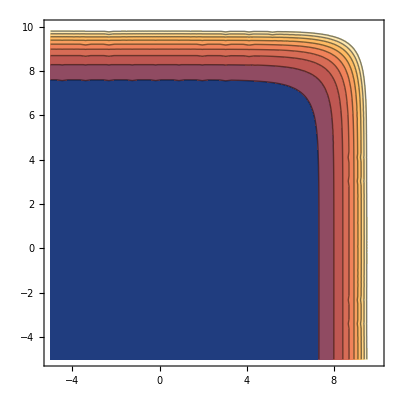

```mathematica
ContourPlot[ⅇ^p+(4 ⅇ^q)/3-p-(2 q)/3,{q,-5,10},{p,-5,10}]
```

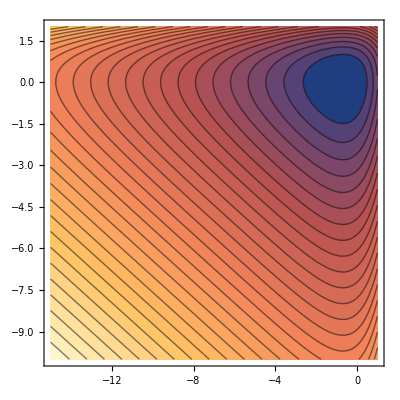

```mathematica
(* α = 2/3, β = 4/3, γ = δ = 1*)
(* These parameters are the ones used in the paper, Figure 1 *)
ContourPlot[1 ⅇ^p-1 p+4/3 Exp[q]-2/3 q,{q,-15,1},{p,-10,2},Contours->30]
```

### (#2.1.2): Trying to Solve for the Bounding Functions:

#### (#2.1.2.1): Seeing how many Solutions are found for the Implicit Equation:

```mathematica
FullSimplify[
Solve[ConstE==LVHamiltonian[q,p],p]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[ConstE+q α+p γ==ⅇ^q β+ⅇ^p δ,p]

Only one solution is found... That is likely because, although we specified that α, β, γ, and δ are positive, we did not specify their relative differences.

```mathematica
LVHamiltonian[q,p]/.p->-(ConstE+q α-ⅇ^q β+γ ProductLog[0,-(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ])/γ//Simplify
```

ConstE

```mathematica
LVHamiltonian[q,p]/.p->-(ConstE+q α-ⅇ^q β+γ ProductLog[1,-(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ])/γ//Simplify
```

ConstE

Wow! It actually works. Nice!

#### (#2.1.2.2): Manually Entering the Solutions We Got:

```mathematica
pPlus=(-ConstE+β Exp[q]-α q)/γ-ProductLog[0,δ/γ Exp[(-ConstE+β Exp[q]-α q)/γ]];
pMinus=(-ConstE+β Exp[q]-α q)/γ-ProductLog[1,δ/γ Exp[(-ConstE+β Exp[q]-α q)/γ]];
```

#### (#2.1.2.3): Since the first integral is just over 1, the integrand for the next integral is just p^+-p^-. So, what is that?

```mathematica
FullSimplify[
pPlus-pMinus
]
```

-ProductLog[(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ]+ProductLog[1,(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ]

#### (#2.1.2.4): Test Run Using a Dummy Integrand, ∫dx (-W_0(x)+W_1(x)):

Below, x stands for the insane thing in the ProductLog[].

```mathematica
FullSimplify[
Integrate[
-ProductLog[0,x]+ProductLog[1,x],
{x, a, b}],
Assumptions->a>0&&b>0&&b>a]
```

ⅇ^ProductLog[a]-ⅇ^ProductLog[b]-ⅇ^ProductLog[1,a]+ⅇ^ProductLog[1,b]+a ProductLog[a]-b ProductLog[b]-a ProductLog[1,a]+b ProductLog[1,b]

#### (#2.1.2.5): Evaluate just the exponentials...

```mathematica
Integrate[Exp[x],x]
Integrate[Exp[Exp[x]]Exp[c x],x]
Integrate[Exp[Exp[x]]Exp[x],x]
```

ⅇ^x

∫ⅇ^(ⅇ^x+c x)ⅆx

ⅇ^(ⅇ^x)

```mathematica
Series[Exp[c x],{x,0,5}]
```

1+c x+(c^2 x^2)/2+(c^3 x^3)/6+(c^4 x^4)/24+(c^5 x^5)/120+O[x]^6

```mathematica
Integrate[Exp[Exp[x]]Series[Exp[c x],{x,0,5}],x]
```

ⅇ x+1/2 (1+c) ⅇ x^2+1/6 (2+2 c+c^2) ⅇ x^3+1/24 (5+6 c+3 c^2+c^3) ⅇ x^4+1/120 (15+20 c+12 c^2+4 c^3+c^4) ⅇ x^5+1/720 (52+75 c+50 c^2+20 c^3+5 c^4+c^5) ⅇ x^6+O[x]^7

```mathematica
Integrate[ProductLog[0,Exp[x]],x]
Integrate[ProductLog[0,Exp[Exp[x]]Exp[c x]],x]
Integrate[ProductLog[0,Exp[Exp[x]]Exp[x]],x]
```

ProductLog[ⅇ^x]+1/2 ProductLog[ⅇ^x]^2

∫ProductLog[ⅇ^(ⅇ^x+c x)]ⅆx

∫ProductLog[ⅇ^(ⅇ^x+x)]ⅆx

Differentiate under the integral?

```mathematica
D[ProductLog[0,Exp[Exp[x]]Exp[c x]],c]
```

(x ProductLog[ⅇ^(ⅇ^x+c x)])/(1+ProductLog[ⅇ^(ⅇ^x+c x)])

```mathematica
Integrate[D[ProductLog[0,Exp[Exp[x]]Exp[c x]],c],x]
```

∫(x ProductLog[ⅇ^(ⅇ^x+c x)])/(1+ProductLog[ⅇ^(ⅇ^x+c x)])ⅆx

This is an identity: https://en.wikipedia.org/wiki/Lambert_W_function#Calculus

```mathematica
FullSimplify[ProductLog[ⅇ^(ⅇ^x+c x)]/(1+ProductLog[ⅇ^(ⅇ^x+c x)]),Assumptions->x∈Reals&&c∈PositiveReals]
```

1-1/(1+ProductLog[ⅇ^(ⅇ^x+c x)])

```mathematica
D[x/(Exp[x]+a),x]//FullSimplify
```

(a-ⅇ^x (-1+x))/((a+ⅇ^x)^2)

```mathematica
Integrate[(a-ⅇ^x (-1+x))/((a+ⅇ^x)^2)/.a->0,x]
```

ⅇ^-x x

#### (#2.1.2.56): Evaluate just the exponentials...

### (#2.1.3): Let’s briefly take a simpler approach:

#### (#2.1.3.1): Solving for the Boundaries using Kerner’s Hamiltonian:

```mathematica
FullSimplify[
Solve[ConstE==γ(Exp[p]-p) + α(Exp[q]-q),p]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[ConstE+q α+p γ==ⅇ^q α+ⅇ^p γ,p]

Again, it won’t actually know for us if there are two solutions or not...

#### (#2.1.3.2): Manually entering the solutions:

```mathematica
pPlusDimensionless=-1/γ(ConstE+(-ⅇ^q+q) α+γ ProductLog[0,-ⅇ^(-(ConstE-ⅇ^q α+q α)/γ)]);
pMinusDimensionless=-1/γ(ConstE+(-ⅇ^q+q) α+γ ProductLog[1,-ⅇ^(-(ConstE-ⅇ^q α+q α)/γ)]);
```

Checking it:

```mathematica
γ(Exp[p]-p) + α(Exp[q]-q)/.p->pPlusDimensionless//FullSimplify
γ(Exp[p]-p) + α(Exp[q]-q)/.p->pMinusDimensionless//FullSimplify
```

ConstE

ConstE

#### (#2.1.3.3): Constructing the integrand:

```mathematica
FullSimplify[
pPlusDimensionless-pMinusDimensionless
]
```

-ProductLog[-ⅇ^(-(ConstE-ⅇ^q α+q α)/γ)]+ProductLog[1,-ⅇ^(-(ConstE-ⅇ^q α+q α)/γ)]

#### (#2.1.3.4): But the W(e^(e^x+x)) thing is still too difficult for the notebook to do analytically!

```mathematica
Integrate[
-ProductLog[-ⅇ^(-(ConstE-ⅇ^q α+q α)/γ)],
{q, 5,6}
]
```

∫_5^6 -ProductLog[-ⅇ^(-(ConstE-ⅇ^q α+q α)/γ)]ⅆq

#### (#2.1.3.5): We are going to try numerical integration to compare!

First of all, what is the numerical integral?

```mathematica
NIntegrate[
ProductLog[0,D[Exp[Exp[q]],q]],
{q, 5,6}
]
```

255.016

Next, what is the numerical solution to what we think the integral is:

```mathematica
N[Exp[6]-Exp[5]]
```

255.016

Let’s compare the difference:

```mathematica
(* This is the numerical error in the integral evaluation: *)
Table[NIntegrate[ProductLog[0,D[Exp[Exp[q]],q]],{q,1,a}]-N[Exp[a]-Exp[1]],{a,1,11}]
```

{0.,3.55271×10^-15,2.13163×10^-14,8.52651×10^-14,2.55795×10^-13,6.25278×10^-13,1.81899×10^-12,4.54747×10^-12,1.27329×10^-11,3.63798×10^-11,8.73115×10^-11}

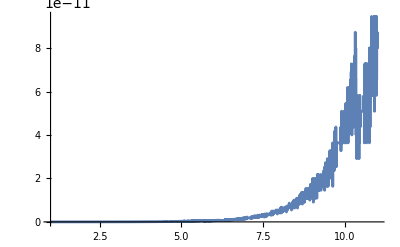

```mathematica
Plot[NIntegrate[ProductLog[0,D[Exp[Exp[q]],q]],{q, 1,a}]-N[Exp[a]-Exp[1]],{a,1,11},PlotRange->All]
```

Doing the integral hinged upon the following identity:

```mathematica
FullSimplify[ProductLog[0,x Exp[x]],Assumptions->x∈PositiveReals]
```

x

From the Wikipedia page: https://en.wikipedia.org/wiki/Lambert_W_function#Identities
Since f(x) = xex is not injective, it does not always hold that W(f(x)) = x, much like with the inverse trigonometric functions.

```mathematica
FullSimplify[ProductLog[0,Exp[x Exp[x]]],Assumptions->x∈PositiveReals]
```

ProductLog[ⅇ^(ⅇ^x x)]

```mathematica
FullSimplify[-Exp[-(ConstE-ⅇ^q α+q α)/γ]+Exp[-ConstE/γ]Exp[(ⅇ^q α-q α)/γ],Assumptions->α∈PositiveReals&&γ∈PositiveReals]
```

0

```mathematica
-Exp[-(ConstE-ⅇ^q α+q α)/γ]+Exp[-ConstE/γ]Exp[α/γ(ⅇ^q -q) ]//FullSimplify
```

0

```mathematica
FullSimplify[-Exp[-(ConstE-ⅇ^q α+q α)/γ]+Exp[-ConstE/γ]Exp[Log[Exp[α/γ]](ⅇ^q -q) ],Assumptions->α∈PositiveReals&&γ∈PositiveReals]
```

0

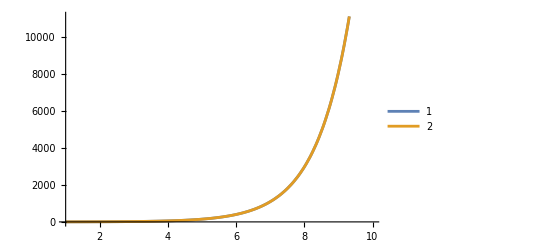

```mathematica
Plot[{ProductLog[0,Exp[Exp[x]+x]],Exp[x]},{x,1,10},PlotLegends->Automatic]
```

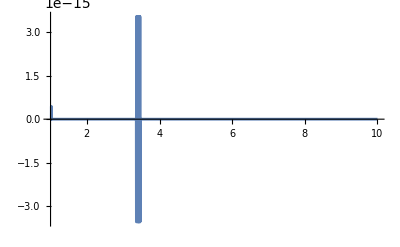

```mathematica
Plot[{ProductLog[0,Exp[Exp[x]+x]]-Exp[x]},{x,1,10},PlotLegends->Automatic]
```

#### (#2.1.3.6): Alright... so, it’s actually a trivial integral and we made it harder than it should have been:

```mathematica
FullSimplify[ProductLog[0,Exp[Exp[x]+x]],Assumptions->x∈PositiveReals]
```

ProductLog[ⅇ^(ⅇ^x+x)]

```mathematica
Solve[y Exp[y]==x,y]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→ProductLog[x]}}

```mathematica
Solve[Exp[y]Exp[Exp[y]]==x,y]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Log[x]-ProductLog[x]}}

```mathematica
Solve[Exp[y+Exp[y]]==x,y]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Log[x]-ProductLog[x]}}

## (#2.2): Suppose it’s an “ecological ideal gas,” where no q is featured in H:

We pretend that, just for computation’s sake, that there is no q in the Hamiltonian, or rather that q only ranges from 0 to some fixed “box” size of length L.

### (#2.2.1): Solving for the maximum value p can take with a fixed E:

```mathematica
Solve[ConstE==δ Exp[p]-γ p ,p]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[ConstE==-p γ+ⅇ^p δ,p]

#### (#2.2.1.1): Verifying the upper bound is correct:

```mathematica
δ Exp[p]-γ p /.p->(-ConstE-γ ProductLog[0,-(ⅇ^(-ConstE/γ) δ)/γ])/γ//Simplify
```

ConstE

#### (#2.2.1.2): Verifying the lower bound is correct:

```mathematica
δ Exp[p]-γ p /.p->(-ConstE-γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])/γ//Simplify
```

ConstE

#### (#2.2.1.3): What happens when E is quite small? Does it go back to something like √(2mE)?

```mathematica
Series[(-ConstE-γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])/γ,{ConstE,0,1}]//FullSimplify
```

-ProductLog[1,-δ/γ]-ConstE/(γ+γ ProductLog[1,-δ/γ])+O[ConstE]^2

#### (#2.2.1.4): Want to see the contours:

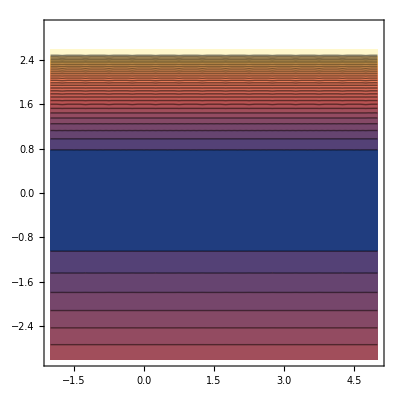

```mathematica
ContourPlot[1 ⅇ^p-1 p,{q,-2,5},{p,-3,3},Contours->30]
```

#### (#2.2.1.5): How about the contours with very small q?

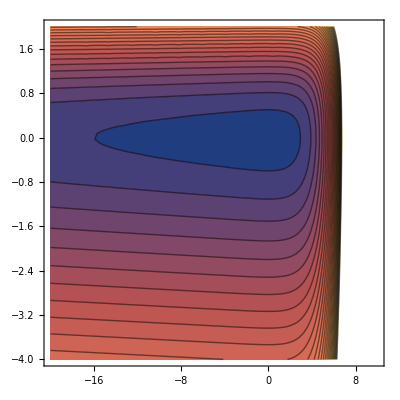

```mathematica
ContourPlot[1 ⅇ^p-1 p+0.01Exp[q]-0.01q,{q,-20,10},{p,-4,2},Contours->30]
```

#### (#2.2.1.6): Same thing except for small p:

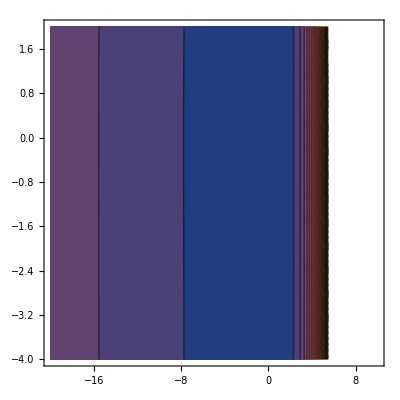

```mathematica
ContourPlot[0.01 ⅇ^p-0.01p+1Exp[q]-1 q,{q,-20,10},{p,-4,2},Contours->30]
```

### (#2.2.2): Let’s now construct the bounding box, bounded specifically by a “volume” of length L:

#### (#2.2.2.1): Computation of Γ(E):

```mathematica
FullSimplify[
2((-ConstE-γ ProductLog[0,-(ⅇ^(-ConstE/γ) δ)/γ])/γ*(-ConstE-γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])/γ)/(Δq Δp)]
```

(2 (ConstE+γ ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ]) (ConstE+γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ]))/(γ^2 Δp Δq)

#### (#2.2.2.2): Computation of g(E)=(dΓ(E))/dE:

```mathematica
FullSimplify[
D[(2 (ConstE+γ ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ]) (ConstE+γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ]))/γ^2,{ConstE,1}]
]
```

(2 (ConstE/(1+ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ])+(γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])/(1+ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ])+(ConstE+γ ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ])/(1+ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])))/γ^2

Let me quickly rewrite this thing:

```mathematica
2/γ^2((ConstE+γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])/(1+ProductLog[0,-(ⅇ^(-ConstE/γ) δ)/γ])+(ConstE+γ ProductLog[0,-(ⅇ^(-ConstE/γ) δ)/γ])/(1+ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ]))-FullSimplify[
D[(2 (ConstE+γ ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ]) (ConstE+γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ]))/γ^2,{ConstE,1}],
Assumptions->ConstE∈Reals&&α∈Reals&&β∈Reals&&γ∈Reals&&δ∈Reals
]
```

-(2 (ConstE/(1+ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ])+(γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])/(1+ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ])+(ConstE+γ ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ])/(1+ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])))/γ^2+(2 ((ConstE+γ ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ])/(1+ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])+(ConstE+γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])/(1+ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ])))/γ^2

## (#2.3): Now suppose that the momentum is quadratic but the potential is the normal U(q):

### (#2.3.1): Making a plot for visualizing the orbits:

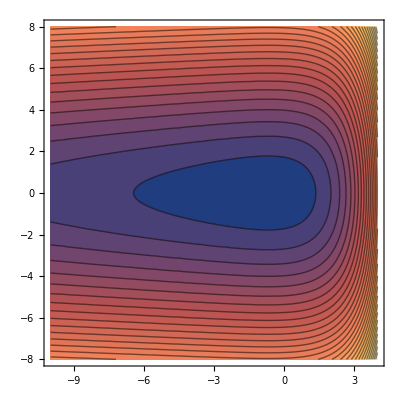

```mathematica
(* α = 2/3, β = 4/3, γ = δ = 1*)
(* These parameters are the ones used in the paper, Figure 1 *)
ContourPlot[δ p^2+β Exp[q]-α q/.α->2/3/.β->4/3/.γ->1/.δ->1,{q,-10,4},{p,-8,8},Contours->30]
```

### (#2.3.2): Trying to Solve for the Bounding Functions:

#### (#2.3.2.1): Seeing how many Solutions are found for the Implicit Equation:

```mathematica
FullSimplify[
Solve[ConstE==δ p^2+β Exp[q]-α q,p]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[ConstE+q α==ⅇ^q β+p^2 δ,p]

Let’s now check to see if we get the right results:

```mathematica
δ p^2+β Exp[q]-α q/.p->-(√(ConstE+q α-ⅇ^q β))/(√δ)//Simplify
```

ConstE

```mathematica
δ p^2+β Exp[q]-α q/.p->+(√(ConstE+q α-ⅇ^q β))/(√δ)//Simplify
```

ConstE

The two solutions differ by the ± sign, and the momentum is squared, so these will of course give the same thing, namely ConstE.

#### (#2.3.2.2): Manually Entering the Solutions We Got:

```mathematica
microPPlus=(√(ConstE+q α-ⅇ^q β))/(√δ);
microPMinus=-(√(ConstE+q α-ⅇ^q β))/(√δ);
```

#### (#2.3.2.3): Since the first integral is just over 1, the integrand for the next integral is just p^+-p^-. So, what is that?

```mathematica
FullSimplify[
microPPlus-microPMinus]
```

2 √((ConstE+q α-ⅇ^q β)/δ)

#### (#2.3.2.4): Let’s do a test run with the integral over q, just to see if it is possible:

```mathematica
FullSimplify[
Integrate[(2 √(ConstE+q α-ⅇ^q β))/(√δ),{q, a, b}],
Assumptions->a∈PositiveReals&&b∈PositiveReals&&b>a
]
```

$Aborted

Rewriting...

```mathematica
√(ConstE+q α-ⅇ^q β)-√(-β(Exp[q]-α/β q-ConstE/β))//FullSimplify
```

```mathematica
FullSimplify[
Integrate[2/(√δ)√(-β(Exp[q]-α/β q-ConstE/β)),{q, a, b}],
e..
]
```

```mathematica
Series[Sqrt[1+x],{x,0,5}]
```

```mathematica
FullSimplify[Series[Sqrt[Exp[x]-x-1],{x,0,5}],Assumptions->x∈Reals]
```

## (#3): Canonical Ensemble Analysis:

## (#3.1): Partition Function:

### (#3.1.1): Defining the entire Partition Function:

```mathematica
LVZ[σ_]:=Exp[-σ LVHamiltonian[q,p]]
```

### (#3.1.2): Defining the Z_p Part:

```mathematica
LVZp[σ_]:=Exp[-σ(δ Exp[p]-γ p)]
```

### (#3.1.3): Defining the Z_q Part:

```mathematica
LVZq[σ_]:=Exp[-σ(β Exp[q]-α q)]
```

### (#3.1.4): Integrating the Z_p Part:

```mathematica
LVZpIntegral=Integrate[LVZp[σ],{p,-∞,∞}]
```

### (#3.1.5): Integrating the Z_q Part:

```mathematica
LVZqIntegral=Integrate[LVZq[σ],{q,-∞,∞}]
```

### (#3.1.6): Cross-checking: Z_p Z_q should equal Z:

```mathematica
LVZIntegral=Integrate[LVZ[σ],{q,-∞,∞},{p,-∞,∞}]
```

We need to confirm that the result is the same as doing the single integral all at once.

```mathematica
LVZpIntegral LVZqIntegral - LVZIntegral
```

### (#3.1.7): Plotting Z(σ) with some test parameters:

According to the [following link on the Wiki page about the LV equations](https://en.wikipedia.org/wiki/Lotka%E2%80%93Volterra_equations#Phase-space_plot_of_a_further_example), there are closed cycles for α = 2/3, β = 4/3, γ = 1, and δ = 1. So, let’s use those values while checking these plots.

#### (#3.1.7.1): Plotting Z(σ) with test parameters:

```mathematica
Plot[
LVZIntegral/.α->2/3/.β->4/3/.γ->1/.δ->1,
{σ,0,20},
PlotStyle->Red
]
```

#### (#3.1.7.2): Plotting Z(T) — remember that σ = 1/(k_B T)—with test parameters:

```mathematica
Plot[
LVZIntegral/.α->2/3/.β->4/3/.γ->1/.δ->1/.σ->1/T,
{T,0.01,1.00},
PlotStyle->Red
]
```

## (#3.2): Average Energy, ⟨E⟩=-∂/(∂ β)log(Z):

### (#3.2.1): Quantitative calculation using the standard formula:

```mathematica
LVEnergyAverage=-D[Log[LVZIntegral],σ]//FullSimplify
```

Just need to check if I can simplify this with another form:

```mathematica
(α(1+Log[β σ]-PolyGamma[0,α σ])+γ(1+Log[δ σ]-PolyGamma[0,γ σ]) )-LVEnergyAverage//FullSimplify
```

### (#3.2.2): Plotting ⟨E⟩(σ) with some test parameters:

#### (#3.2.2.1): Plotting ⟨E⟩(σ.) with test parameters:

```mathematica
Plot[
LVEnergyAverage/.α->2/3/.β->4/3/.γ->1/.δ->1,
{σ,0.01,2},
PlotStyle->Red,
AxesLabel->{"σ [inverse temperature]","⟨E⟩(σ)"}
]
```

#### (#3.2.2.2): Plotting ⟨E⟩(T) — remember that σ = 1/(k_B T)—with test parameters:

[NOTE]: It appears there is no minimum average energy.

```mathematica
Plot[
LVEnergyAverage/.α->2/3/.β->4/3/.γ->1/.δ->1/.σ->1/T,
{T,-1,3},
PlotStyle->Red,
AxesLabel->{"T [temperature]","⟨E⟩(T)"},
PlotRange->{{-0.5,2.5},{0,6}}
]
```

At zero temperature, the average energy is not zero. So, can we find the value of the thing at T = 0?
First, let’s get the analytical expression in terms of Temperature:

```mathematica
LVEnergyAverage/.σ->1/T
```

Now, obviously evaluating this for T = 0 will lead to divergences. So, let’s determine its value numerically with a very small value for T.

```mathematica
LVEnergyAverage/.σ->1/T/.T->0.0000000000000000001
```

That looks like it corresponds with what the plot is showing. Alright. Good check.

Next, let’s take a limit.

```mathematica
Limit[LVEnergyAverage/.σ->1/T,T->0]
```

Riiiight. That’s expected. [NOTE]: And it turns out that it actually has to do with the direction of the limit! That is, we need to take the limit from the right!
Let’s just try to copy/paste the analytical thing we got earlier:

```mathematica
Limit[
α+γ+α Log[β/T]+γ Log[δ/T]-α PolyGamma[0,α/T]-γ PolyGamma[0,γ/T],
T->0,
(* This strange word means "take limit from the right" *)
 Direction->-1]
```

This should match with the earlier result, so their difference should be 0:

```mathematica
Limit[α+γ+α Log[β/T]+γ Log[δ/T]-α PolyGamma[0,α/T]-γ PolyGamma[0,γ/T],T->0,Direction->-1]-Limit[LVEnergyAverage/.σ->1/T,T->0, Direction->-1]
```

Can we see if this is the number that appears on the plot earlier:

```mathematica
N[α+γ-α Log[α]+α Log[β]-γ Log[γ]+γ Log[δ]/.α->2/3/.β->4/3/.γ->1/.δ->1]
```

Yes, that actually looks about right...

Let’s find the low-temperature behavior by expanding E(T) about T = 0.

```mathematica
Series[LVEnergyAverage/.σ->1/T,{T,0,1}]
```

Oh, nuts. There is some parameter thing going on here... Seems like the heat-capacity may become imaginary if γ in relation to T is not nice...

```mathematica
Limit[α+γ-α Log[α/T]+α Log[β/T]-γ Log[γ/T]+γ Log[δ/T]+T,T->0,Direction->-1]
```

```mathematica
Plot[
(α+γ-α Log[α/T]+α Log[β/T]-γ Log[γ/T]+γ Log[δ/T])+T/.α->2/3/.β->4/3/.γ->1/.δ->1,
{T,0,0.5},
PlotStyle->Red,
AxesLabel->{"T [temperature]","⟨E⟩(T)"}
]
```

## (#3.3): Variance of Average Energy, ⟨(ΔE)^2⟩=-(∂⟨E⟩)/(∂β)=(∂^2 ln(Z))/(∂β^2):

### (#3.3.1): Quantitative calculation using the standard formula:

```mathematica
LVEnergyVariance=-D[LVEnergyAverage,σ]//FullSimplify
```

Check the above against the other formula:

```mathematica
LVEnergyVariance-D[Log[LVZIntegral],{σ,2}]//FullSimplify
```

Is there really no dependence on β or δ?

```mathematica
D[Log[LVZIntegral],{σ,2}]//FullSimplify
```

### (#3.3.2): Plotting ⟨(ΔE)^2⟩(σ) with some test parameters:

#### (#3.3.2.1): Plotting ⟨(ΔE)^2⟩(σ) with test parameters:

```mathematica
Plot[
LVEnergyVariance/.α->2/3/.β->4/3/.γ->1/.δ->1,
{σ,0.01,2},
PlotStyle->Red,
AxesLabel->{"σ","⟨(ΔE)^2⟩(σ)"}
]
```

#### (#3.2.2.2): Plotting ⟨(ΔE)^2⟩(T) — remember that σ=1/(k_B T)—with test parameters:

```mathematica
Plot[
LVEnergyVariance/.α->2/3/.β->4/3/.γ->1/.δ->1/.σ->1/T,
{T,0,10},
PlotStyle->Red,
AxesLabel->{"T","⟨(ΔE)^2⟩(T)"}
]
```

#### (#3.2.2.3): Using Manipulate[] to see how things change with α and γ:

```mathematica
Manipulate[
Plot[
-T (α+γ-(α^2 PolyGamma[1,α/T])/T-(γ^2 PolyGamma[1,γ/T])/T),
{T,0.0001,10},
PlotStyle->Red,
AxesLabel->{"T","⟨(ΔE)^2⟩(T)"}
],{α,0.01,10.0},{γ,0.01,10.0}]
```

#### (#3.2.2.4): Zero-Temperature Limit:

```mathematica
Limit[LVEnergyVariance/.σ->1/T,T->0,Direction->-1]
```

It is probably the Trigamma Function thing sending things to 0 here.

```mathematica
Limit[ PolyGamma[1,α/T],T->0,Direction->-1]
```

## (#3.4): “Heat” Capacity, C_v=⟨(ΔE)^2⟩/(k_B T^2):

### (#3.4.1): Quantitative calculation using the standard formula:

```mathematica
LVHeatCapacity=σ^2 LVEnergyVariance//FullSimplify
```

```mathematica
LVHeatCapacity/.σ->1/T
```

#### (#3.4.1): High-temperature limit:

First try a limit:

```mathematica
Limit[LVHeatCapacity/.σ->1/T,T->∞]
```

#### (#3.4.2): Low-temperature limit:

First try a limit:

```mathematica
Limit[LVHeatCapacity/.σ->1/T,T->0]
```

Series expansion around T = 0 to first order:

```mathematica
Series[LVHeatCapacity/.σ->1/T,{T,0,1},Assumptions->T∈Reals&&α∈Reals&&β ∈Reals&&γ∈Reals&&δ∈Reals]
```

Series expansion around T = 0 to second order:

```mathematica
Series[LVHeatCapacity/.σ->1/T,{T,0,2},Assumptions->T∈PositiveReals&&α∈Reals&&β ∈Reals&&γ∈Reals&&δ∈Reals]
```

### (#3.4.2): Plotting C_v(σ) with some test parameters:

#### (#3.4.2.1): Plotting C_v(σ) with test parameters:

```mathematica
Plot[
LVHeatCapacity/.α->2/3/.β->4/3/.γ->1/.δ->1,
{σ,0.001,100},
PlotStyle->Red,
AxesLabel->{"σ","C(σ)"}
]
```

#### (#3.4.2.2): Plotting C_v(T) — remember that σ = 1/(k_B T)—with test parameters:

```mathematica
Plot[
LVHeatCapacity/.α->2/3/.β->4/3/.γ->1/.δ->1/.σ->1/T,
{T,0.0001,40},
PlotStyle->Red,
AxesLabel->{"T","C_V(T)"},
PlotRange->{{-3,20},{2.5,-0.1}}
]
```

Wow. It appears to asymptote to 2. I did not expect that. Let’s use a Manipulate[] function to verify that the boundary points of the curve do not change when we vary the parameters.

```mathematica
Manipulate[
Plot[
(-α-γ+(α^2 PolyGamma[1,α/T])/T+(γ^2 PolyGamma[1,γ/T])/T)/T,
{T,0.0001,40},
PlotStyle->Red,
AxesLabel->{"T","C_V(T)"},
PlotRange->{{-3,20},{2.5,-0.1}}
],{α,0.01,10.0},{γ,0.01,10.0}]
```

#### (#3.4.2.3): Trying to compute ΔS = (∫_T1)^T2 dT(C_v(T))/T :

```mathematica
(LVHeatCapacity/.σ->1/T)/T//FullSimplify
```

```mathematica
ChangeInLVEntropy=Integrate[
(-T (α+γ)+α^2 PolyGamma[1,α/T]+γ^2 PolyGamma[1,γ/T])/T^3,{T,T1,T2},
Assumptions->T1∈PositiveReals&&T2∈PositiveReals&&α∈PositiveReals&&γ∈PositiveReals&&T2>T1
]
```

Can it do the integral of the PolyGamma only?

```mathematica
Integrate[ PolyGamma[1,α/T],{T,T1,T2},Assumptions->T1∈PositiveReals&&T2∈PositiveReals&&α∈PositiveReals&&T2>T1]
```

No it can’t. How about if we do PolyGamma over T?

```mathematica
Integrate[PolyGamma[1,α/T]/T,{T,T1,T2},Assumptions->T1∈PositiveReals&&T2∈PositiveReals&&α∈PositiveReals&&T2>T1]
```

Can’t do that either. Now, I think for PolyGamma over T^2 it can actually solve it:

```mathematica
Integrate[PolyGamma[1,α/T]/T^2,{T,T1,T2},Assumptions->T1∈PositiveReals&&T2∈PositiveReals&&α∈PositiveReals&&T2>T1]
```

It can do PolyGamma over T^2. But notice it cannot do PolyGamma over T^3:

```mathematica
Integrate[PolyGamma[1,α/T]/T^3,{T,T1,T2},Assumptions->T1∈PositiveReals&&T2∈PositiveReals&&α∈PositiveReals&&T2>T1]
```

And, just for fun, let’s try PolyGamma over T^4:

```mathematica
Integrate[PolyGamma[1,α/T]/T^4,{T,T1,T2},Assumptions->T1∈PositiveReals&&T2∈PositiveReals&&α∈PositiveReals&&T2>T1]
```

```mathematica
ChangeInLVEntropy=NIntegrate[1/T(-α-γ+(α^2 PolyGamma[1,α/T])/T+(γ^2 PolyGamma[1,γ/T])/T)/T/.α->2/3/.γ->1,{T,0.001,100.0}]
ChangeInLVEntropy=NIntegrate[1/T(-α-γ+(α^2 PolyGamma[1,α/T])/T+(γ^2 PolyGamma[1,γ/T])/T)/T/.α->2/4/.γ->1,{T,0.001,100.0}]
ChangeInLVEntropy=NIntegrate[1/T(-α-γ+(α^2 PolyGamma[1,α/T])/T+(γ^2 PolyGamma[1,γ/T])/T)/T/.α->2/5/.γ->1,{T,0.001,100.0}]
```

## (#3.5): Entropy, S=-k_B θ^2∂/(∂θ)(ln(Z))/θ:

### (#3.5.1): Quantitative calculation using the standard formula:

```mathematica
LVEntropy=FullSimplify[
-σ^2 D[ Log[LVZIntegral]/σ,σ]
]
```

Check against another formula: S = ⟨E⟩/T+ k_B ln(Z) or S=k_B(β ⟨E⟩ + ln(Z))

```mathematica
LVEntropy-(σ LVEnergyAverage+ Log[LVZIntegral])//FullSimplify
```

In terms of temperature:

```mathematica
LVEntropy/.σ->1/T//FullSimplify
```

Yeah. It doesn’t do much... Let me see something else (just another algebraic rewriting):

```mathematica
FullSimplify[
((α+γ+T (Log[Gamma[α/T]]+Log[Gamma[γ/T]])-α PolyGamma[0,α/T]-γ PolyGamma[0,γ/T])/T)-(LVEntropy/.σ->1/T)
]
```

#### (#3.5.1.1): High-temperature limit:

First try a limit:

```mathematica
Limit[LVEntropy/.σ->1/T//FullSimplify,T->∞]
```

Now try to expand:

```mathematica
Series[LVEntropy/.σ->1/T,{T,Infinity,1},]
```

#### (#3.5.1.2): Low-temperature limit:

Try a limit first:

```mathematica
Limit[LVEntropy/.σ->1/T//FullSimplify,T->0]
```

Now try to expand it to O(T):

```mathematica
Series[LVEntropy/.σ->1/T,{T,0,1}]
```

Try to expand to O(T^2):

```mathematica
Series[LVEntropy/.σ->1/T,{T,0,2}]
```

#### (#3.5.1.3): If the Entropy crosses 0 at some finite T, we should be able to figure out where that is:

```mathematica
Solve[(α+γ+γ Log[δ/T])/T+Log[(δ/T)^(-γ/T) Gamma[α/T] Gamma[γ/T]]-(α PolyGamma[0,α/T]+γ PolyGamma[0,γ/T])/T==0,{T}]
```

```mathematica
Reduce[(α+γ+γ Log[δ/T])/T+Log[(δ/T)^(-γ/T) Gamma[α/T] Gamma[γ/T]]-(α PolyGamma[0,α/T]+γ PolyGamma[0,γ/T])/T==0,{T}]
```

```mathematica
FindRoot[(α+γ+γ Log[δ/T])/T+Log[(δ/T)^(-γ/T) Gamma[α/T] Gamma[γ/T]]-(α PolyGamma[0,α/T]+γ PolyGamma[0,γ/T])/T,{T,1}]
```

### (#3.5.2): Plotting S(θ) with some test parameters:

#### (#3.5.2.1): Plotting S(θ) with test parameters:

```mathematica
Plot[
LVEntropy/.α->2/3/.β->4/3/.γ->1/.δ->1,
{σ,0.01,10},
PlotStyle->Red,
AxesLabel->{"σ [inverse temperature]","S(σ)"}
]
```

#### (#3.5.2.2): Plotting S(T) — remember that σ=1/(k_B T)—with test parameters:

```mathematica
Plot[
LVEntropy/.α->2/3/.β->4/3/.γ->1/.δ->1/.σ->1/T,
{T,0.01,2},
PlotStyle->Red,
AxesLabel->{"T [temperature]","S(T)"}
]
```

I need to see this: is there a bound for the entropy...

```mathematica
Plot[
LVEntropy/.α->2/3/.β->4/3/.γ->1/.δ->1/.σ->1/T,
{T,0.006,0.1},
PlotStyle->Red,
AxesLabel->{"T [temperature]","S(T)"}
]
```

The major question is: Does the 0 point actually move, or is it for some random reason universal, the way the heat capacity behaved?

```mathematica
Plot[
LVEntropy/.α->1.1/.β->0.4/.γ->0.4/.δ->0.1/.σ->1/T,
{T,0.01,2},
PlotStyle->Red,
AxesLabel->{"T","S(T)"}
]
```

The 0 of the entropy has moved, indicating that there is in principle a nontrivial inverse problem to solve for this critical value of the temperature...

### (#3.5.2): Entropy of Mixing:

Entropy is an equilibrium (additive!) state function. So, let’s compare the entropy before and after mixing of two systems at the same temperature:

```mathematica
CombinedSystemsLVEntropy=σ (αC+γC+γC Log[δC σ])+Log[(δC σ)^(-γC σ) Gamma[αC σ] Gamma[γC σ]]-σ (αC PolyGamma[0,αC σ]+γC PolyGamma[0,γC σ]);
TwoSeparatedSystemsLVEntropy=(σ (α1+γ1+γ1 Log[δ1 σ])+Log[(δ1 σ)^(-γ1 σ) Gamma[α1 σ] Gamma[γ1 σ]]-σ (α1 PolyGamma[0,α1 σ]+γ1 PolyGamma[0,γ1 σ]))+(σ (α2+γ2+γ2 Log[δ2 σ])+Log[(δ2 σ)^(-γ2 σ) Gamma[α2 σ] Gamma[γ2 σ]]-σ (α2 PolyGamma[0,α2 σ]+γ2 PolyGamma[0,γ2 σ]));
```

```mathematica
FullSimplify[CombinedSystemsLVEntropy-TwoSeparatedSystemsLVEntropy]
```

### (#3.5.3): Entropy as Temperature Changes?

Remember how we couldn’t do the integral for ΔS = ∫dT (C(T))/T? Let’s try to do it now:

```mathematica
FullSimplify[(LVEntropy/.σ->1/T2)-(LVEntropy/.σ->1/T1),T1∈PositiveReals&&T2∈PositiveReals]
```

First of all, it is astounding that the dependence on β and δ just goes away in this derivative... Obviously, it’s just math, but it is nonetheless wildly unexpected.

```mathematica
D[LVEntropy/.σ->1/T,T]//FullSimplify
```

```mathematica
FullSimplify[D[LVEntropy/.σ->1/T,T],]
```

Rewriting using some algebra:

```mathematica
(D[LVEntropy/.σ->1/T,T])-(1/T(-α-γ+(α^2 PolyGamma[1,α/T])/T+(γ^2 PolyGamma[1,γ/T])/T)/T)//FullSimplify
```

Yup. It’s the same.

## (#3.6): Free Energy, F=-k_BT log(Z):

### (#3.6.1): Quantitative calculation using the standard formula:

```mathematica
LVFreeEnergy=-1/σ Log[LVZIntegral]//FullSimplify
```

### (#3.6.2): Plotting F(θ) with some test parameters:

#### (#3.6.2.1): Plotting F(θ) with test parameters:

```mathematica
Plot[
LVFreeEnergy/.α->2/3/.β->4/3/.γ->1/.δ->1,
{σ,-1.0,10.0},
PlotStyle->Red,
AxesLabel->{"σ","F(σ)"}
]
```

#### (#3.6.2.2): Where is it crossing 0?

```mathematica
LVFreeEnergy/.α->2/3/.β->4/3/.γ->1/.δ->1
```

```mathematica
NSolve[-Log[2^(-4 σ/3) 3^(2 σ/3) σ^(-5 σ/3) Gamma[(2 σ)/3] Gamma[σ]]/σ==0,σ]
```

#### (#3.6.2.3): Plotting F(T) — remember that θ = 1/(k_B T)—with test parameters:

```mathematica
Plot[
LVFreeEnergy/.α->2/3/.β->4/3/.γ->1/.δ->1/.σ->1/T,
{T,0.01,1},
PlotStyle->Red,
AxesLabel->{"T","F(T)"}
]
```

#### (#3.6.2.4): Where is it crossing 0?

```mathematica
LVFreeEnergy/.α->2/3/.β->4/3/.γ->1/.δ->1/.σ->1/T
```

```mathematica
NSolve[-T Log[2^(-4/3/T) 3^(2/3/T) (1/T)^(-5/3/T) Gamma[2/(3 T)] Gamma[1/T]]==0,T]
```

### (#3.6.3): Verifying that indeed C_V=-T (∂^2)_T F holds here:

Yup, it works:

```mathematica
FullSimplify[-T(D[LVFreeEnergy/.σ->1/T,{T,2}])-LVHeatCapacity/.σ->1/T]
```

### (#3.6.4): Derivatives of F(T) with respect to “microscopic parameters”

#### (#3.6.4.1): ((∂F(T))/(∂α))_(T,β,γ,δ):

```mathematica
D[LVFreeEnergy/.σ->1/T,α]//FullSimplify
```

Check for discontinuities:

```mathematica
Plot[
D[LVFreeEnergy/.σ->1/T,α]/.α->2/3/.β->4/3/.γ->1/.δ->1,
{T,0.1,10},
PlotStyle->Red,
AxesLabel->{"T","(∂F)/(∂α)(T)"}
]
```

#### (#3.6.4.2): ((∂F(T))/(∂β))_(T,α,γ,δ):

```mathematica
D[LVFreeEnergy/.σ->1/T,β]//FullSimplify
```

This is obviously flat:

```mathematica
Plot[
D[LVFreeEnergy/.σ->1/T,β]/.α->2/3/.β->4/3/.γ->1/.δ->1,
{T,0.1,10},
PlotStyle->Red,
AxesLabel->{"T","(∂F)/(∂β)(T)"}
]
```

#### (#3.6.4.3): ((∂F(T))/(∂γ))_(T,α,β,δ):

Should be extremely similar to (#3.6.4.1):

```mathematica
D[LVFreeEnergy/.σ->1/T,γ]//FullSimplify
```

#### (#3.6.4.4): ((∂F(T))/(∂δ))_(T,α,β,γ):

Should be γ/δ:

```mathematica
D[LVFreeEnergy/.σ->1/T,δ]//FullSimplify
```

## (#3.X): Information Geometry:

#### (#3.X.Y): Fischer Information Metric:

The metric is one-dimensional because there is only one Lagrange multiplier in the Partition Function above.

```mathematica
FischerMetric11LV=D[-Log[LVZIntegral],{θ, 2}]//FullSimplify
```

## (#4): Corresponding “Maxwell-Boltzmann Velocity Distribution”

## (#4.1): “Making” it a Probability Distribution:

```mathematica
Integrate[cp LVZp[σ],{p,-∞,∞},Assumptions->cp ∈Reals]
```

Now fix the constant:

```mathematica
MaxBoltMomentumDistribution=1/((δ σ)^(-γ σ) Gamma[γ σ])LVZp[σ];
```

### (#4.1.1): Mean Momentum:

```mathematica
Integrate[p^1 MaxBoltMomentumDistribution,{p,-∞,∞}]
```

### (#4.1.2): Most Probable Momentum:

```mathematica
Solve[D[MaxBoltMomentumDistribution,p]==0,p]
```

### (#4.1.3): Other Moments:

```mathematica
Integrate[p^n MaxBoltMomentumDistribution,{p,-∞,∞},Assumptions->n∈PositiveIntegers]
```

## (#X): Keeping the Rotation Angle ϕ Open:

## (#X.1): Transforming to the Hamiltonian:

### (#X.1.1): Original Dynamical Invariant:

```mathematica
LVDynInvariant=δ x - γ Log[x]+β y-α Log[y];
```

### (#X.1.2): Verifying original coordinate transformation works:

```mathematica
FullSimplify[
LVHamiltonian[q,p]-LVDynInvariant/.y->Exp[q]/.x->Exp[p],
Assumptions->x∈Reals&&y∈Reals&&q∈Reals&&p∈Reals]
```

### (#X.1.3): Now, do the original transformation for (x, y) and (q, p) was for ϕ=π/4:

Must understand that we flipped the “chirality” when we assigned q to log(y) and p to log(x), and that’s why we have flipped the order of the logs in this column vector below:

```mathematica
RotationMatrix[π/4].{Log[y],Log[x]}//MatrixForm
```

### (#X.1.4): Here is then the arbitrary transformation between (x, y) and (q, p) for any ϕ:

```mathematica
RotationMatrix[ϕ].{Log[y],Log[x]}//MatrixForm
```

```mathematica
Solve[
{p==Cos[ϕ] Log[x]+Log[y] Sin[ϕ],q==Cos[ϕ] Log[y]-Log[x] Sin[ϕ]},
{x,y}]
```

```mathematica
FullSimplify[
LVDynInvariant/.y->ⅇ^(-(-p Csc[ϕ]-q Cot[ϕ] Csc[ϕ])/(1+Cot[ϕ]^2))/.x->ⅇ^(-(-p Cos[ϕ]+q Sin[ϕ])/(Cos[ϕ]^2+Sin[ϕ]^2)),
Assumptions->q∈Reals&&p∈Reals&&ϕ∈Reals
]
```

## (#X.2): Constructing the Canonical Ensemble Partition Function:

### (#X.2.1): Arbitrary Angle Hamiltonian:

```mathematica
LVRotatedHamiltonian[q_,p_,ϕ_]:=ⅇ^(q Cos[ϕ]+p Sin[ϕ]) β+ⅇ^(p Cos[ϕ]-q Sin[ϕ]) δ-(q α+p γ) Cos[ϕ]+(-p α+q γ) Sin[ϕ];
```

Quickly checking that this generalizes the previous Hamiltonian at ϕ = 0;

```mathematica
FullSimplify[
LVRotatedHamiltonian[q,p,0]-LVHamiltonian[q,p]
]
```

### (#X.2.2): Arbitrary Angle Canonical Ensemble Partition Function:

```mathematica
LVRotatedZ[σ_]:=Exp[-σ LVRotatedHamiltonian[q,p,ϕ]];
```

### (#X.2.3): Attempting Integration of the Arbitrary ϕ Partition Function:

```mathematica
LVRotatedZIntegral=Integrate[
LVRotatedZ[σ],{q,-∞,∞},{p,-∞,∞},
Assumptions->ϕ∈Reals
]
```